### MateX y Funciones

```mathematica
<<MaTeX`
flogticks[y1_,y2_]:=Module[{table1,table2},
table1={};
Do[
Do[
AppendTo[table1,{i*10^j,""}];
,{i,1,9,1}]
,{j,y1,y2}];
table2=Table[{10^j,ToString[10]^ToString[j]},{j,y1,y2}];
Do[
If[table2[[k,1]]==1,table2=ReplacePart[table2,{k,2}->1]],
{k,1,Length@table2}];
Join[table1,table2]
]
hnlchain="/home/sane/mainhnlchain/hnlchain/";
```

### PARÁMETROS

```mathematica
totald431=20*10*10^6;
d431pPOT=1.2*10^-6;
ncm2=700*300;
ncm2=1;
POTpyear=1.47*10^21;
(*POTpyear=10^20;*)
d431factor=1;
d431factor=1/totald431*d431pPOT*POTpyear*1/ncm2
```

8.82×10^6

### MaTeX

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
latexnue=MaTeX["\\nu_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumu=MaTeX["\\nu_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutau=MaTeX["\\nu_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
latexnuebar=MaTeX["\\bar{\\nu}_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumubar=MaTeX["\\bar{\\nu}_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutaubar=MaTeX["\\bar{\\nu}_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["E_{\\nu} \\text{(GeV)}",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["\\nu/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
ylabelbar=MaTeX["\\bar{\\nu}/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
```

# BACKGROUND

## Parámetros

```mathematica
totald431=20*10*10^6;
d431pPOT=1.2*10^-6;
ncm2=700*300;
ncm2=1;
POTpyear=1.47*10^21;
(*POTpyear=10^20;*)
d431factor=1/totald431*d431pPOT
d431factor=1/totald431*d431pPOT*POTpyear*1/ncm2
d431factor=1
```

6.×10^-15

8.82×10^6

1

## Importar Data

```mathematica
(* IMPORTA DATA A LAS TABLAS bgnutable & bgnutablebar *)
fbgimport[idGun_]:=Module[{idGuns,nudata,nubardata,nutable,nubartable,bwidth,xrange},
Switch[idGun,
	431, idGuns="431",
	-431, idGuns="431bar",
	411, idGuns="411",
	-411, idGuns="411bar",
	421, idGuns="421",
	-421, idGuns="421bar"
];
nudata=Import[hnlchain<>"bg/analysis-bg/"<>idGuns<>"-e.dat"];
nubardata=Import[hnlchain<>"bg/analysis-bg/"<>idGuns<>"-ebar.dat"];
nutable={};
Do[
bwidth=(nudata[[i,3]]-nudata[[i,2]])/nudata[[i,1]];
xrange=N[Table[nudata[[i,2]]+q*bwidth,{q,0,nudata[[i,1]]}]];
AppendTo[nutable,N[Table[{xrange[[l]],nudata[[i,3+l]]/bwidth*d431factor},{l,1,nudata[[i,1]]}]]];
,{i,1,41*3}];
nubartable={};
Do[
bwidth=(nubardata[[i,3]]-nubardata[[i,2]])/nubardata[[i,1]];
xrange=N[Table[nubardata[[i,2]]+q*bwidth,{q,0,nubardata[[i,1]]}]];
AppendTo[nubartable,N[Table[{xrange[[l]],nubardata[[i,3+l]]/bwidth*d431factor},{l,1,nubardata[[i,1]]}]]];
,{i,1,41*3}];
Do[
Do[
If[nutable[[i,j,2]]==0,nutable=ReplacePart[nutable,{i,j,2}->0.1]]
,{j,1,Length@nutable[[i]]}],
{i,1,Length@nutable}];
Do[
Do[
If[nubartable[[i,j,2]]==0,nubartable=ReplacePart[nubartable,{i,j,2}->0.1]]
,{j,1,Length@nubartable[[i]]}],
{i,1,Length@nubartable}];
AppendTo[bgnutable,nutable];
AppendTo[bgnutablebar,nubartable];
];
(* LLAMAR LA DATA-TABLE *)
fbgtable[idGun_,offaxis_,flavour_]:=Module[{},
	Switch[idGun,
		431, bgnutable[[1,offaxis*3+flavour]],
		-431, bgnutable[[2,offaxis*3+flavour]],
		411, bgnutable[[3,offaxis*3+flavour]],
		-411, bgnutable[[4,offaxis*3+flavour]],
		421, bgnutable[[5,offaxis*3+flavour]],
		-421, bgnutable[[6,offaxis*3+flavour]]
	]
];
fbgtablebar[idGun_,offaxis_,flavour_]:=Module[{},
	Switch[idGun,
		431, bgnutablebar[[1,offaxis*3+flavour]],
		-431, bgnutablebar[[2,offaxis*3+flavour]],
		411, bgnutablebar[[3,offaxis*3+flavour]],
		-411, bgnutablebar[[4,offaxis*3+flavour]],
		421, bgnutablebar[[5,offaxis*3+flavour]],
		-421, bgnutablebar[[6,offaxis*3+flavour]]
	]
];
(* IMPORTAR DATA *)
bgnutable={};
bgnutablebar={};
Do[
	fbgimport[idGun]
,{idGun,{431}}];
```

## Plots nu

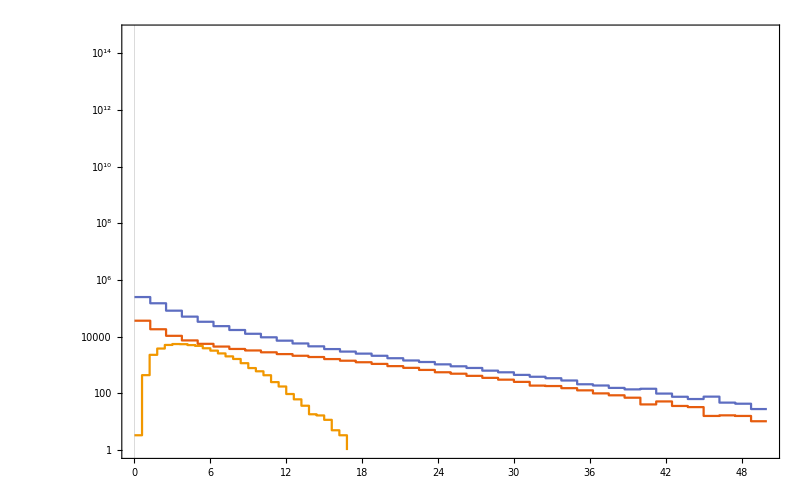

/home/sane/mainhnlchain/plots/energy-0.pdf

```mathematica
idGun=431;
offaxis =0;
latext1=MaTeX["\\text{Off-axis="<>ToString[NumberForm[offaxis,{2,1}]]<>" m}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.05,0.9}],{-1,0}]];
framelabel={xlabel,ylabel};
frametickstyle=Directive[Black];
plotstyle=Opacity[1.0];
imagesize={300,Automatic};
plotrange={{0,50},{1,5*10^14}};
yticks=flogticks[0,14];
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
legends={latexnue,latexnumu,latexnutau};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.1],{0.9,0.82}];
plot1=ListStepPlot[{fbgtable[idGun,offaxis,1],fbgtable[idGun,offaxis,2],fbgtable[idGun,offaxis,3]},PlotTheme->"Scientific",FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->White,FrameTicks->frameticks];
plotexp=Show[plot1,text]
Export[NotebookDirectory[]<>"energy-"<>ToString[offaxis]<>".pdf",plotexp]
```

## Plots nubar

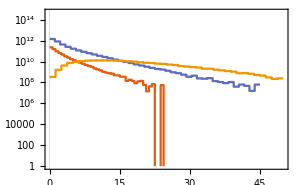

/home/sane/mainhnlchain/plots/energybar-0.pdf

```mathematica
idGun=431;
offaxis=0;
latext1=MaTeX["\\text{Off-axis="<>ToString[NumberForm[offaxis,{2,1}]]<>" m}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.05,0.9}],{-1,0}]];
framelabel={xlabel,ylabelbar};
legends={latexnuebar,latexnumubar,latexnutaubar};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.1],{0.9,0.82}];
plotstyle={Opacity[1.0]};
yticks=flogticks[0,14];
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
plot2=ListStepPlot[{fbgtablebar[idGun,offaxis,1],fbgtablebar[idGun,offaxis,2],fbgtablebar[idGun,offaxis,3]},PlotTheme->"Scientific",FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->White,FrameTicks->frameticks];
plotexp=Show[plot2,text]
Export[NotebookDirectory[]<>"energybar-"<>ToString[offaxis]<>".pdf",plotexp]
```

# SIGNAL

## d431

### Main Parameters

```mathematica
idGunString = "431";
totald431=10*10*10^6;
d431pPOT=1.2*10^-6;
ncm2=700*300;
ncm2=1;
POTpyear=1.47*10^21;
(*POTpyear=10^20;*)
d431factor=1;
d431factor=1/totald431*d431pPOT*POTpyear*1/ncm2
```

1.764×10^7

### Data

```mathematica
(* IMPORT DATA *)
nudata=Import[hnlchain<>"dirac/meson/analysis/431-e.dat"];
nubardata=Import[hnlchain<>"dirac/meson/analysis/431-ebar.dat"];
(* CREAR TABLA {BIN_Xmin, BINCONTENT} NU *)
nutable={};
Do[
bwidth=(nudata[[i,3]]-nudata[[i,2]])/nudata[[i,1]];
xrange=N[Table[nudata[[i,2]]+q*bwidth,{q,0,nudata[[i,1]]}]];
AppendTo[nutable,N[Table[{xrange[[l]],nudata[[i,3+l]]/bwidth*d431factor},{l,1,nudata[[i,1]]}]]];
,{i,1,15*41*3}];
(* CREAR TABLA {BIN_Xmin, BINCONTENT} NUBAR *)
nubartable={};
Do[
bwidth=(nubardata[[i,3]]-nubardata[[i,2]])/nubardata[[i,1]];
xrange=N[Table[nubardata[[i,2]]+q*bwidth,{q,0,nubardata[[i,1]]}]];
AppendTo[nubartable,N[Table[{xrange[[l]],nubardata[[i,3+l]]/bwidth*d431factor},{l,1,nubardata[[i,1]]}]]];
,{i,1,15*41*3}];
(* CORREGIR EN CASO BINCONTENT==0 *)
Do[
Do[
If[nutable[[i,j,2]]==0,nutable=ReplacePart[nutable,{i,j,2}->0.1]]
,{j,1,Dimensions[nutable[[i]]][[1]]}];
Do[
If[nubartable[[i,j,2]]==0,nubartable=ReplacePart[nubartable,{i,j,2}->0.1]]
,{j,1,Dimensions[nubartable[[i]]][[1]]}];
,{i,1,15*41*3}];
(* DEFINIR FUNCIONES PARA PLOTEO *)
f[mhnl_,offaxis_,flavour_]:=nutable[[IntegerPart[41*3*(mhnl-0.5)/0.1+3*offaxis+flavour+0.001]]];
fbar[mhnl_,offaxis_,flavour_]:=nubartable[[IntegerPart[41*3*(mhnl-0.5)/0.1+3*offaxis+flavour+0.001]]];
```

### MaTeX

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
magnificationtext=0.9;
latexnue=MaTeX["\\nu_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumu=MaTeX["\\nu_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutau=MaTeX["\\nu_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
latexnuebar=MaTeX["\\bar{\\nu}_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumubar=MaTeX["\\bar{\\nu}_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutaubar=MaTeX["\\bar{\\nu}_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["E_{\\nu} \\text{(GeV)}",Magnification->magnificationaxes,ContentPadding->False];
ylabelcm2=MaTeX["\\nu/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["\\nu/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
ylabelbarcm2=MaTeX["\\bar{\\nu}/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];ylabelbar=MaTeX["\\bar{\\nu}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
```

### Plots nu

```mathematica
plot[mhnl_,offaxis_]:=Module[{latext1,latext2,text1,text2,framelabel,frametickstyle,plotstyle,imagesize,plotrange,yticks,xticks,frameticks,legends,plotlegends,plot1,plotexp,filename},
latext1=MaTeX["\\text{mHNL = "<>ToString[NumberForm[mhnl,{2,1}]]<>" GeV}",Magnification->magnificationtext,ContentPadding->False];
latext2=MaTeX["\\text{off-axis = "<>ToString[NumberForm[offaxis,{2,1}]]<>" m}",Magnification->magnificationtext,ContentPadding->False];
text1=Graphics[Text[latext1,Scaled[{0.05,0.9}],{-1,0}]];
text2=Graphics[Text[latext2,Scaled[{0.05,0.825}],{-1,0}]];
framelabel={xlabel,ylabel};
frametickstyle=Directive[Black];
plotstyle=Opacity[1.0];
imagesize={300,Automatic};
plotrange={{0,50},{1,6*10^5}};
yticks={{10^1,"10"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"}};
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
legends={latexnue,latexnumu,latexnutau};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.1],{0.9,0.82}];
plot1=ListStepPlot[{f[mhnl,offaxis,1],f[mhnl,offaxis,2],f[mhnl,offaxis,3]},PlotTheme->"Scientific",FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->White,FrameTicks->frameticks];
plotexp=Show[plot1,text1,text2];
filename=NotebookDirectory[]<>ToString[idGunString]<>"-e-"<>ToString[NumberForm[mhnl,{2,1}]]<>"-"<>ToString[NumberForm[offaxis,{2,1}]]<>".pdf";
Export[filename,plotexp];
Print[filename];
plotexp
];
```

/home/sane/mainhnlchain/plots/431-e-0.5-0.pdf

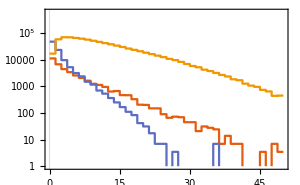

```mathematica
plot[0.5,0]
```

### Plots nubar

```mathematica
plotbar[mhnl_,offaxis_]:=Module[{latext1,latext2,text1,text2,framelabel,frametickstyle,plotstyle,imagesize,plotrange,yticks,xticks,frameticks,legends,plotlegends,plot1,plotexp,filename},
latext1=MaTeX["\\text{mHNL = "<>ToString[NumberForm[mhnl,{2,1}]]<>" GeV}",Magnification->magnificationtext,ContentPadding->False];
latext2=MaTeX["\\text{off-axis = "<>ToString[NumberForm[offaxis,{2,1}]]<>" m}",Magnification->magnificationtext,ContentPadding->False];
text1=Graphics[Text[latext1,Scaled[{0.05,0.9}],{-1,0}]];
text2=Graphics[Text[latext2,Scaled[{0.05,0.825}],{-1,0}]];
framelabel={xlabel,ylabelbar};
frametickstyle=Directive[Black];
plotstyle=Opacity[1.0];
imagesize={300,Automatic};
plotrange={{0,50},{1,6*10^5}};
yticks={{10^1,"10"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"}};
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
legends={latexnuebar,latexnumubar,latexnutaubar};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.1],{0.9,0.82}];
plot1=ListStepPlot[{fbar[mhnl,offaxis,1],fbar[mhnl,offaxis,2],fbar[mhnl,offaxis,3]},PlotTheme->"Scientific",FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->White,FrameTicks->frameticks];
plotexp=Show[plot1,text1,text2];
filename=NotebookDirectory[]<>ToString[431]<>"-ebar-"<>ToString[NumberForm[mhnl,{2,1}]]<>"-"<>ToString[NumberForm[offaxis,{2,1}]]<>".pdf";
Export[filename,plotexp];
Print[filename];
plotexp
];
```

/home/sane/mainhnlchain/hnlchain/dirac/meson/analysis/431-ebar-0.5-25.pdf

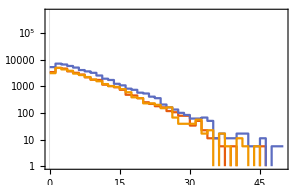

```mathematica
plotbar[0.5,25]
```

```mathematica
Do[
plotbar[i,0],{i,0.5,1.9,0.1}]
```

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-0.5-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-0.6-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-0.7-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-0.8-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-0.9-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.0-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.1-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.2-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.3-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.4-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.5-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.6-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.7-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.8-0.pdf

/home/sane/mainhnlchain/dirac/120/meson2hnl/analysis/ebar-1.9-0.pdf